```mathematica
<<AceFEM`;
```

Import the prediction to be visualised.

```mathematica
input = Import["examples/2dlshapemagnet.csv"];
nn=input[[All,2]] ;
fem = input[[All,3]] ;
error = input[[All,4]];
list = Partition[error, 2];
nodeerror = (Norm/@list) ;
```

Setup the domain as used while generating the dataset.

```mathematica
SMTInputData[];
L=6;H=2;H2=6/7;nx=12;ny=3; nx2=3; ny2=7;
ntx = nx+nx2; nty = ny2;
points={{0,0},{4*L/5,0},{4*L/5,H2},{0,H2}};
points2={{4*L/5,0},{L,0},{L,H},{4*L/5,H}};
SMTAddDomain["Ω","OL:SEPEQ1DFHYQ1NeoHooke",{"E *"->500,"ν *"->0.4}];
SMTAddEssentialBoundary["X"==0&,1->0,2->0];
SMTAddMesh[Polygon[points],"Ω","Q1",{nx,ny}];
SMTAddMesh[Polygon[points2],"Ω","Q1",{nx2,ny2}];
SMTAnalysis[]; 
mrest = SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->False,"Mesh"->Gray,"FillElements"->False,"ImageSize"->300];
```

Visualise FEM and NN Predictions

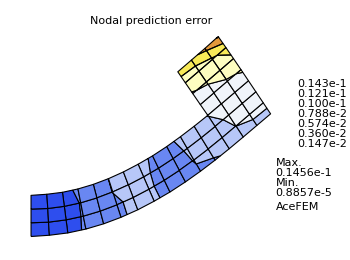
-Graphics- -Graphics-

```mathematica
(*Assign true FEM solutions. Red mesh*)
SMTNodeData["at",Partition[fem ,2]];
mfem=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Red,"FillElements"->False,"ImageSize"->300];

(*Assign neural network predictions. Blue mesh*)
SMTNodeData["at",Partition[nn,2]];
mnn=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Blue,"FillElements"->False,"ImageSize"->300] ;

(*Plot prediction error*)
errorplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"FillElements"->False,"Field"-> nodeerror,"Mesh"-> Black,"Contour"->{0.00147,0.0143,5},"ImageSize"->350,"Label"-> "Nodal prediction error"] ;

Show[mfem,mnn,mrest]  Show[errorplt]
```